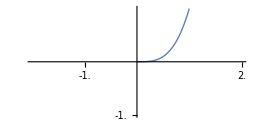
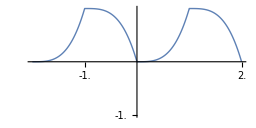
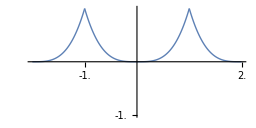
-Graphics-
x^3.35
x^3.35
-Graphics-
0.5 + (-1)^floor(x)*(-0.5 + mod(x, 1)^3.35)
0.5 - 0.5*(-1)^floor(x) + (-1)^floor(x)*mod(x, 1)^3.35
-Graphics-
(1 - mod(x, 1))^3.35*mod(1 + floor(-x), 2) + mod(x, 1)^3.35*mod(1 + floor(x), 2)
(1 - mod(x, 1))^3.35*mod(1 - ceiling(x), 2) + mod(x, 1)^3.35*mod(1 + floor(x), 2)

```mathematica
ᔓᔕ={ (*WorkingPrecision-> 16,*) MaxRecursion-> 2^4-1,PlotPoints-> 1+2^8,AspectRatio-> 1/2,PlotRangePadding-> 1/256, PlotRange-> {{-2,2},{-1,1}},Ticks-> {Range[-4,4,.5],Range[-4,4,.5]},ImageSize-> 256,PlotStyle-> Thin};
ᴥ={X,-2,2};
ꗳ[X_]:=                ((((                X^3.35                ))))                ;
(*ꗳ[X_]:=                ((((                1/(E^(1/X+1/(X-1))+1)                ))))                ;*)
(*ꗳ[X_]:=                ((((                .5*(1+Tanh[(.5-X)/((-1+X)*X)])                ))))                ;*)
(*ꗳ[X_]:=                ((((                ((-32 (Max[0,-15/16+X]^3-Max[0,-13/16+X]^3-Max[0,-11/16+X]^3+Max[0,-9/16+X]^3-Max[0,-7/16+X]^3+Max[0,-5/16+X]^3+Max[0,-3/16+X]^3-Max[0,-1/16+X]^3))/3)                ))))                ;*)
ᑐᑕᗯꗳᗯᑐᑕ[X_]:=(-1)^Floor[X] *(ꗳ[Mod[X,1]]-0.5)+0.5;
ᑐᑕ옷ꗳ옷ᑐᑕ[X_]:=ꗳ[Mod[X,1]] Mod[Floor[X+1],2]+ꗳ[1-Mod[X,1]] Mod[Floor[-X+1],2];
Column[
{
Column[{Plot[ꗳ[X],Evaluate[ᴥ],Evaluate[ᔓᔕ]],ToLowerCase[StringReplace[ToString[ꗳ[X],InputForm],{"]"->")","["->"("}]],ToLowerCase[StringReplace[ToString[Simplify[ExpandAll[ꗳ[X]]],InputForm],{"]"->")","["->"("}]]},Alignment->Center],
Column[{Plot[ᑐᑕᗯꗳᗯᑐᑕ[X],Evaluate[ᴥ],Evaluate[ᔓᔕ]],ToLowerCase[StringReplace[ToString[ᑐᑕᗯꗳᗯᑐᑕ[X],InputForm],{"]"->")","["->"("}]],ToLowerCase[StringReplace[ToString[Simplify[ExpandAll[ᑐᑕᗯꗳᗯᑐᑕ[X]]],InputForm],{"]"->")","["->"("}]]},Alignment->Center],
Column[{Plot[ᑐᑕ옷ꗳ옷ᑐᑕ[X],Evaluate[ᴥ],Evaluate[ᔓᔕ]],ToLowerCase[StringReplace[ToString[ᑐᑕ옷ꗳ옷ᑐᑕ[X],InputForm],{"]"->")","["->"("}]],ToLowerCase[StringReplace[ToString[Simplify[ExpandAll[ᑐᑕ옷ꗳ옷ᑐᑕ[X]]],InputForm],{"]"->")","["->"("}]]},Alignment->Center],
},Alignment->Center]
```